CreateDirectory::filex: C:\Users\Racher\source\repos\sophon\graphics already exists.

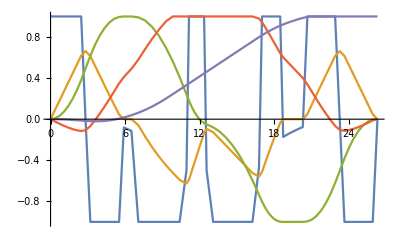
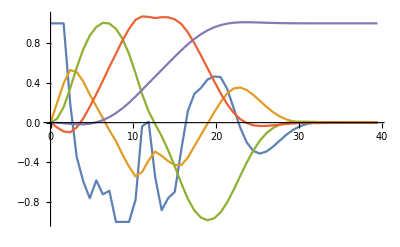
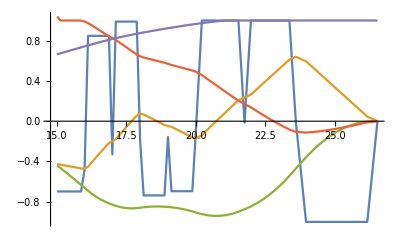

{-Graphics3D-,-Graphics3D-}

```mathematica
outDir="c:\\Users\\Racher\\source\\repos\\sophon\\graphics";
CreateDirectory[outDir];
(*DeleteFile[FileNames["*.pdf",outDir]]*)
savePdf=Function[{fileName,data},Export[FileNameJoin[{outDir,StringReplace[fileName," "->""]<>".pdf"}],data]];
nth={"1st", "2nd","3rd", "4th"};
colors=ColorData[97,"ColorList"];
colors=ColorData[98,"ColorList"];
thickColors={Thick,colors[[#]]}&/@Range[6];
rawlegend={"u","x_0","x_1","x_2","x_3"};
legend=Style[#,Black]&/@rawlegend;
Get["CustomTicks`"]
loadFile=Function[filename,
data=BinaryReadList[FileNameJoin[{NotebookDirectory[],"simdata",filename<>".binary64"}],"Real64"];
pointCount=Round[data[[1]]];
size=Round[data[[2]]];
planCount=Round[data[[3]]];
rowCount=(Length[data]-3)/(5pointCount size);
data=Table[data[[5row size pointCount+5col size+5rank+coord+4]],{rank,0,size-1},{row,0,rowCount-1},{col,0,pointCount-1},{coord,0,4}];
data={data[[All,;;planCount]],data[[All,planCount+1;;]]};
order=Length[data[[1]]]-1;
pointPerSegment=(pointCount-1)/(2^order-1);
Clear[rowCount];
Clear[planCount];
Clear[size];
Clear[pointCount];
data
];
loadFile["rocket"];
(*Animate[
pointss=data[[#,All,All,All,{1,3}]];
xmax=Max[pointss[[1,All,-1,1]]];
ListLinePlot[pointss[[All,n]],ImageSize->Medium,PlotRange->{{0,xmax},{-1.05,1.05}},PlotMarkers->Automatic]
,{n,Range[Dimensions[data[[#]]][[2]]]},AnimationRunning->False]&/@{1,2}*)
ListLinePlot[#]&/@{data[[1,All,10,All,{1,3}]],data[[2,All,All,1,{1,3}]],data[[2,All,20,All,{1,3}]]}
ListPointPlot3D[Flatten[#,{{1},{2,3}}][[All,All,1;;3]]]&/@data
```

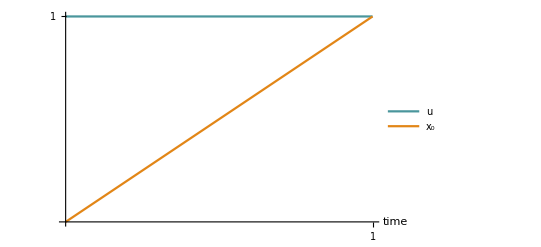
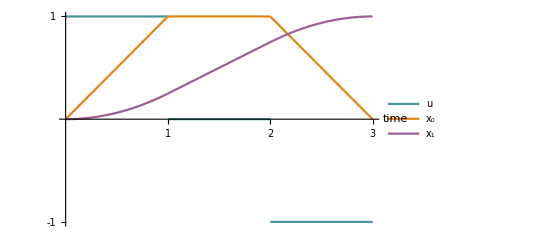
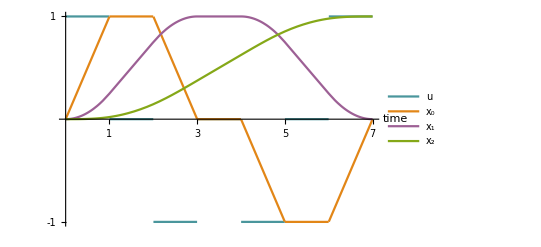

```mathematica
u=Piecewise[{{1, t<1}, {0, t<2}, {-1, t<3}, {0, t<4}, {-1, t<5}, {0, t<6}, {1, t<7}, {0, t<8}, {-1, t<9}, {0, t<10}, {1, t<11}, {0, t<12}, {1, t<13}, {0, t<14}, {-1, t<15}}];
x0=Integrate[u,t];
x1=Integrate[x0,t]0.5;
x2=Integrate[x1,t]0.25;
x3=Integrate[x2,t]0.125;
ux={u,x0,x1,x2,x3};
plotIdeal=Function[{n,tE,off},
plotLabel="Theoretical linear "<>nth[[n]]<>" order solution";
plot=Plot[Evaluate@Take[ux,n+1],{t,0,tE},PlotLegends->Take[legend,n+1],Ticks->{Range[tE],{-1,1}},AxesLabel->{"time"},PlotStyle->thickColors[[off;;]]];
savePdf[plotLabel,plot];
plot
];
{plotIdeal[1,1,1],plotIdeal[2,3,1],plotIdeal[3,7,1]}
```

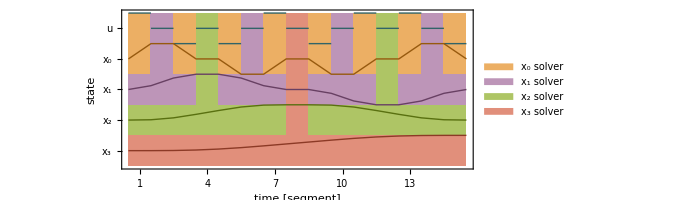

```mathematica
rank=4;
cols=2^rank-1;
tab =Table[0,{i,rank+1},{j,cols}];
For[r=2,r<=rank,r++,
For[i=1,i≤cols,i++,tab[[r+1]][[i]]=r-1];
For[i=2^(r-1),i≤cols,i+=2^(r-1),For[j=1,j≤r,j++,tab[[j]][[i]]=r-1];];
]
lightColors=Lighter[#]&/@colors;
c1=#-1->lightColors[[#+1]]&/@Range[rank];
label="4th order segment tree";
m=Legended[
MatrixPlot[tab,FrameTicks->{Thread[{Range[Length[legend]],legend}],Range[cols]},ColorRules->c1,Axes->True,FrameLabel->{"state","time [segment]"}],
SwatchLegend[lightColors[[2;;rank+1]],Style[rawlegend[[#+1]]<>" solver",Black]&/@Range[rank]]
];
ytrans=Function[{n,p},{p[[1]],5.5-n+p[[2]]/2}];
fps=Function[f,f/.t->#-1&/@(Range[cols+1])][#]&/@ux;
us={{#-1,fps[[1,#]]},{#,fps[[1,#]]}}&/@Range[cols];
us=Function[line,ytrans[1,#]&/@line][#]&/@us;
linecolors=Darker[colors[[#]]]&/@Range[rank+1];
ulines={linecolors[[1]],Line[#]&/@us};
xs=Function[n,{linecolors[[n]],Line[ytrans[n,{#-1,fps[[n,#]]}]&/@Range[cols+1]]}][#+1]&/@Range[rank];
l=Graphics[{ulines,xs}];
s=Show[{m,l}]
savePdf["arrayplot",s];
```

0.317668

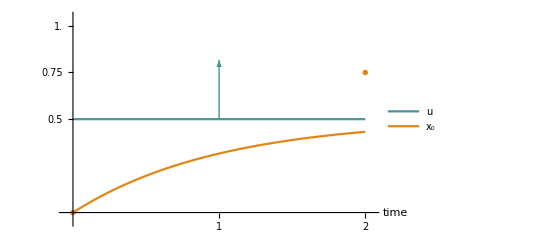
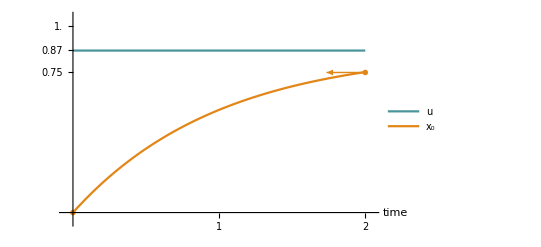
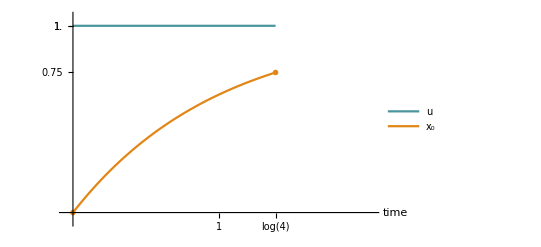

```mathematica
endMarker={Graphics[{colors[[2]],Disk[]}],0.05};
xt=0.75;
te={2,Log[4]};
u={0.5,0.75/(1-E^-2),1};
x0=y[t]/.DSolve[{y'[t]==u[[1]]-y[t],y[0]==0},y[t],t][[1]];
getName=Function[n,label="Theoretical damped 1st order solver figure "<>ToString[n]];
plot=Function[{u,x0,te,n},Plot[{u,x0},{t,0,te},PlotLegends->legend,PlotRange->{{-0.05,2.05},{-.05,1.05}},Ticks->{{1,te},{-1.,0.75,1.,Round[u,0.01]}},AxesLabel->{"time"},PlotStyle->colors]];
dArrowVert=xt-x0/.t->te[[1]]
arrow=Graphics[{colors[[1]],{Arrowheads[Large],Arrow[{{te[[1]]/2,u[[1]]},{te[[1]]/2,u[[1]]+dArrowVert}}]}}];
s1=Show[{ plot[u[[1]],x0,te[[1]],1],ListPlot[{{0,0},{te[[1]],xt}},PlotMarkers->endMarker],arrow}];
x0=y[t]/.DSolve[{y'[t]==0.87-y[t],y[0]==0},y[t],t][[1]];
arrow=Graphics[{colors[[2]],{Arrowheads[Large],Arrow[{{te[[1]],xt},{te[[1]] u[[2]],xt}}]}}];
s2=Show[{ plot[u[[2]],x0,te[[1]],2],ListPlot[{{0,0},{te[[1]],xt}},PlotMarkers->endMarker],arrow}];
range={t,0,1.4};
x0=y[t]/.DSolve[{y'[t]==1-y[t],y[0]==0},y[t],t][[1]];
s3=Show[{plot[u[[3]],x0,te[[2]],3],ListPlot[{{0,0},{te[[2]],xt}},PlotMarkers->endMarker]}];
savePdf[getName[1],s1];
savePdf[getName[2],s2];
savePdf[getName[3],s3];
{s1,s2,s3}
```

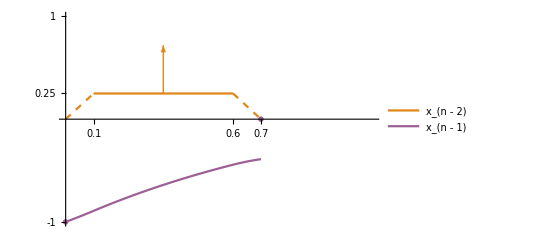
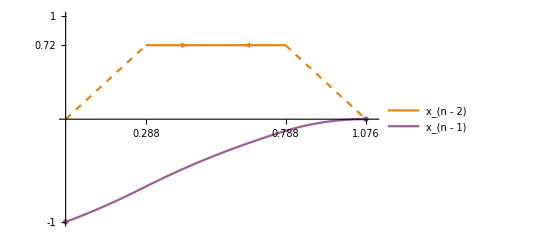
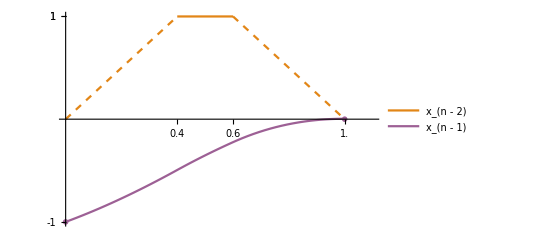

```mathematica
endMarker={Graphics[{colors[[3]],Disk[]}],0.05};
getName=Function[n,label="Theoretical damped higher order solver figure "<>ToString[n]];
plot=Function[n,
ts=xm 0.4;
tt=2ts+tm;
x0=Interpolation[{{0,0},{ts,xm},{ts+tm,xm},{2ts+tm,0}},InterpolationOrder->1];
x1=y/.NDSolve[{y'[t]==x0[t]-y[t],y[0]==-1},y,{t,0,tt}][[1]];
Show[
{
Plot[x0[t],{t,0,ts},PlotStyle->{colors[[2]],Dashed}],
Plot[x0[t],{t,ts,ts+tm},PlotLegends->{Style["x_(n - 2)",Black]},PlotStyle->colors[[2]]],
Plot[x0[t],{t,ts+tm,tt},PlotStyle->{colors[[2]],Dashed}],
Plot[x1[t],{t,0,tt},PlotLegends->{Style["x_(n - 1)",Black]},PlotStyle->colors[[3]]],
ListPlot[{{0,-1},{tt,0}},PlotMarkers->endMarker]
}
,PlotRange->{{0,1.1},{-1,1}},Ticks->{{ts,ts+tm,tt},{-1,xm,1}},AxesLabel->{"time"}]];
getArrow=Function[{ends,color},Graphics[{color,{Arrowheads[Large],Arrow[ends]}}]];
tm=0.5;
xm=0.25;
xm2=0.72;
s1=Show[{plot[1],getArrow[{{ts+tm/2,xm},{ts+tm/2,xm2}},colors[[2]]]}];
xm=xm2;
s2=Show[{plot[2],getArrow[{{ts,xm},{ts+0.15,xm}},colors[[2]]],getArrow[{{ts+tm,xm},{ts+tm-0.15,xm}},colors[[2]]]}];
xm=1;
tm=0.2;
s3=plot[3];
savePdf[getName[1],s1];
savePdf[getName[2],s2];
savePdf[getName[3],s3];
{s1,s2,s3}
```

```mathematica
Range[10][[;;6;;2]]
```

{1,3,5}

```mathematica
createPlanFormation=Function[{filename,max,step,zMin},
loadFile[filename];
ranks=Length[data[[1]]];
shapes=Function[rank,
points=data[[1,rank,1;;max;;step,All,1;;3]];
{colors[[rank]],Thick,{Line[points](*,Point[#]&/@points*)}}
][#]&/@Range[ranks];
label=filename<>" plan formation";
g=Legended[Graphics3D[shapes,
BoxRatios->{60,60,11},
Axes->True,
Ticks->{Automatic,LogTicks[2,0,100,TickLabelStep->2,ShowMinorTicks->False],{-1,0,1}},
AxesLabel->{"time","iteration"},
ImageSize->Medium,
AxesEdge->{{-1,-1},{-1,1},{-1,-1}},
PlotRange->{Automatic,Automatic,{zMin,1.2}}],
LineLegend[Take[colors,ranks],legend]
];
savePdf[label,g];
g
];
{createPlanFormation["O1",9,2,-0.2],
createPlanFormation["O2",9,2,-1.2],
createPlanFormation["O4",9,2,-1.2],
createPlanFormation["O4z",9,2,-1.2]
}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

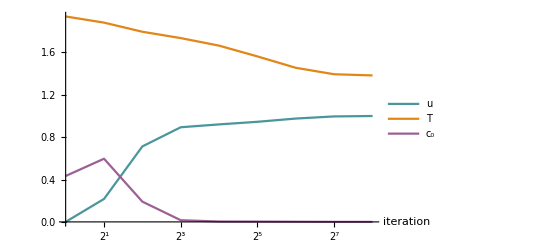

```mathematica
loadFile["O1"];
leg=Style[#,Black]&/@ {"u","T","c_0"};
g=ListLinePlot[data[[1,1,1;;9,1,{2,#}]]&/@{3,4,5},PlotRange->All,Ticks->{{#,2^ToString[#]}&/@Range[10],Automatic},PlotLegends->leg,AxesLabel->{"iteration"},PlotStyle->colors]
savePdf["1st order mdc",g];
```

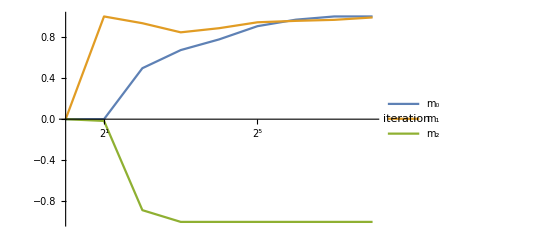
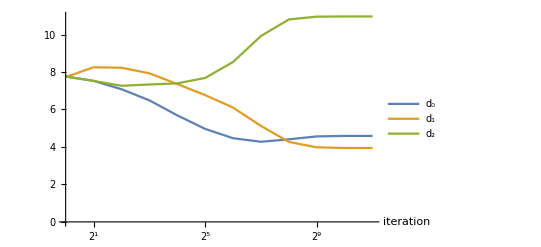
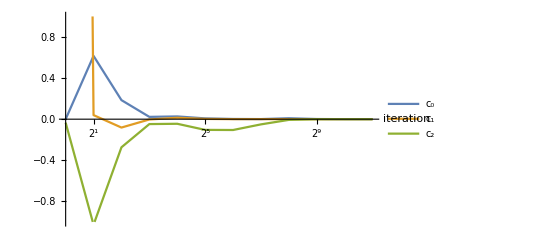

```mathematica
cols=100;
midRanks=Table[0,100];
For[r=0,r<cols,r++,
For[c=2^r-1,c<cols,c=c+2^r,
midRanks[[c+1]]=r]
];
filename="O2";
loadFile[filename];
leg=Style[Subscript["m", #-1],Black]&/@Range[16];
g1=ListLinePlot[data[[1,1+midRanks[[#]],1;;9,2+pointPerSegment(#-1),{2,3}]]&/@Range[3],PlotRange->All,Ticks->{{#,2^ToString[#]}&/@Range[16],Automatic},PlotLegends->leg,AxesLabel->{"iteration"}];
savePdf[filename<>" lower states",g1];
leg=Style[Subscript["d", #-1],Black]&/@Range[16];
g2=ListLinePlot[data[[1,1,All,2+pointPerSegment(#-1),{2,4}]]&/@Range[3],PlotRange->All,Ticks->{{#,2^ToString[#]}&/@Range[16],Automatic},PlotLegends->leg,AxesLabel->{"iteration"}];
savePdf[filename<>" segment durations",g2];
leg=Style[Subscript["c", #-1],Black]&/@Range[16];
g3=ListLinePlot[data[[1,1,All,1+pointPerSegment(#-1),{2,5}]]&/@Range[3],PlotRange->{Automatic,{-1,1}},Ticks->{{#,2^ToString[#]}&/@Range[16],Automatic},PlotLegends->leg,AxesLabel->{"iteration"}];
savePdf[filename<>" correction values",g3];
{g1,g2,g3}
```

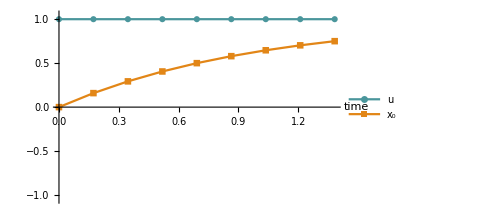
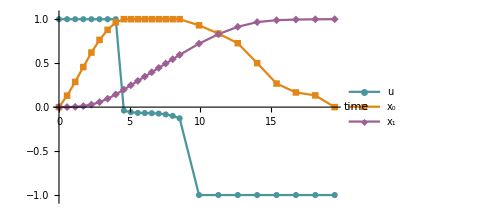
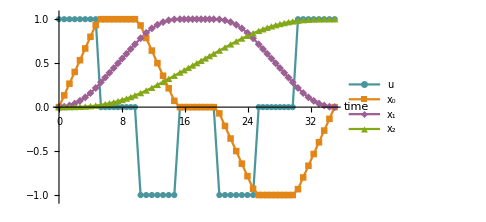
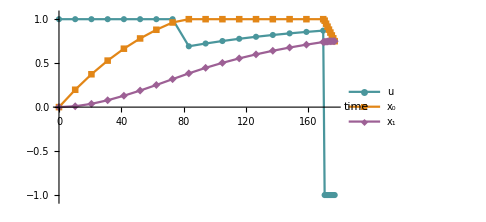
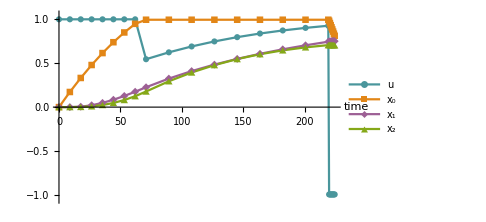
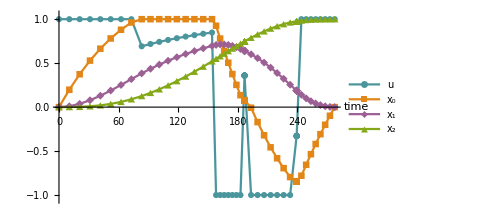
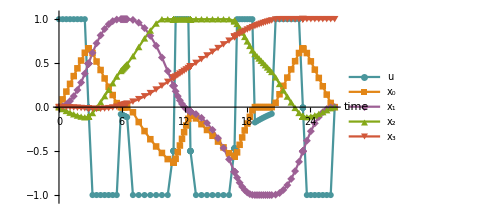

```mathematica
createPlanLast=Function[filename,
loadFile[filename];
label=filename<>" plan iteration "<>ToString[Round[2^data[[1,1,-1,1,2]]]];
p=ListLinePlot[data[[1,All,-1,All,{1,3}]],ImageSize->Medium,PlotRange->{Automatic,{-1.05,1.05}},PlotMarkers->Automatic,PlotLegends->legend,AxesLabel->{"time",None},PlotStyle->colors];
savePdf[label,p];
p
];
{createPlanLast["O1"],
createPlanLast["O2"],
createPlanLast["O3"],
createPlanLast["DC"],
createPlanLast["DCpp"],
createPlanLast["Servo"],
createPlanLast["Rocket"]}
```

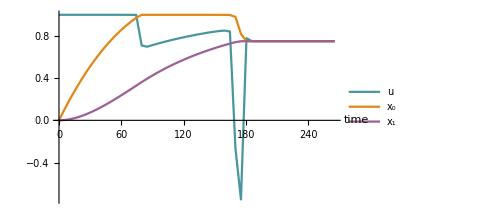
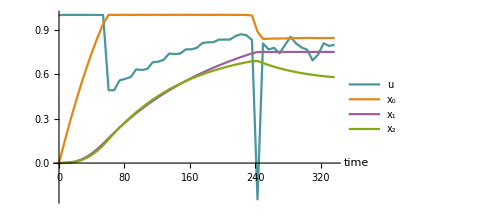
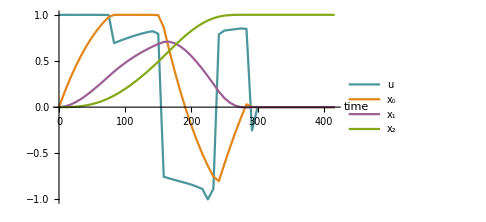
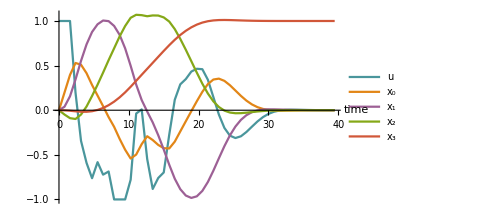
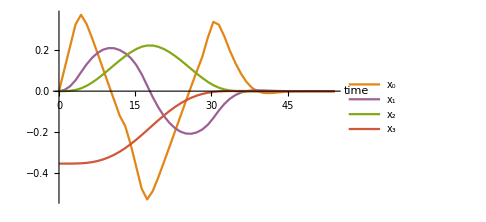

```mathematica
createSim2=Function[{filename,n},
loadFile[filename];
label=filename<>" simulation";
p=ListLinePlot[data[[2,n;;,All,1,{1,3}]],ImageSize->Medium,PlotRange->{Automatic,If[n>0,Automatic,{-1.1,1.1}]},(*PlotMarkers->Automatic,*)PlotLegends->legend[[n;;]],AxesLabel->{"time",None},PlotStyle->colors[[n;;]]];
savePdf[label,p];
p
];
{createSim2["DC",1],
createSim2["DCpp",1],
createSim2["Servo",1],
createSim2["Rocket",1],
createSim2["O4c",2]}
```

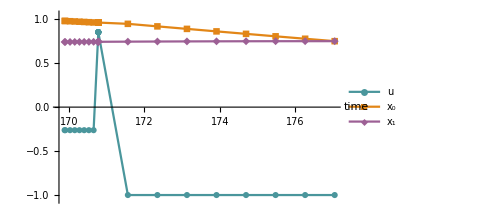

```mathematica
createSimPlanN=Function[{filename,n},
loadFile[filename];
label=filename<>" plan at "<>ToString[data[[2,1,n,1,2]]];
fn=filename<>" plan at "<>ToString[n];
p=ListLinePlot[data[[2,All,n,All,{1,3}]],ImageSize->Medium,PlotRange->{Automatic,{-1.05,1.05}},PlotMarkers->Automatic,PlotLegends->legend,AxesLabel->{"time",None},PlotStyle->colors];
savePdf[fn,p];
p
];
createSimPlanN["DC",33]
```

1.00893

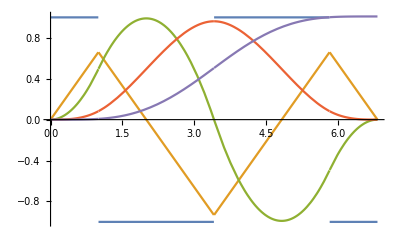

```mathematica
u=Piecewise[{{1, t<1}, {-1, t<2+√2}, {1, t<3+2 √2}, {-1, True}}];
te=4+2 √2;
x0=Integrate[u,t]0.66;
x1=Integrate[x0,t]1.5;
x2=Integrate[x1,t]0.5;
x3=Integrate[x2,t]0.36;
x3/.t->te//N
Plot[{u,x0,x1,x2,x3},{t,0,te}]
```

```mathematica
loadFile["Rocket"];
g=ListPointPlot3D[Flatten[data[[2,1]],1][[All,1;;3]]]
savePdf["Rocket plan change",g];
```

-Graphics3D-

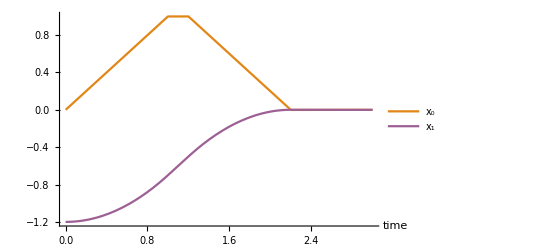

```mathematica
rank=2;
model={
If[{1,0}.x[t]>1,-1,
If[{1,0}.x[t]<-1,1,
Clip[{-500,-1000}.x[t]]
]
],
{1,0}.x[t]};
te=3;
s=x[t]/.First[NDSolve[
{
x'[t]==model,
x[0]=={0,-1.2}
},x,{t,0,te}]];
name="PD large step";
p=Plot[{s[[1]],s[[2]]},{t,0,te},PlotRange->All,AxesLabel->{"time"},PlotLegends->Drop[legend,1],PlotStyle->colors[[2;;3]]]
savePdf[name, p];
```

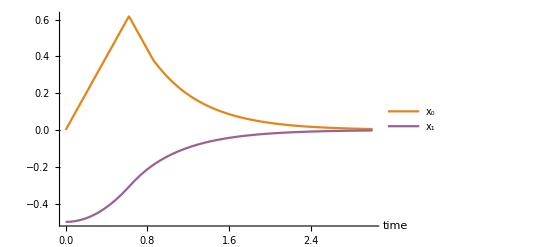

```mathematica
rank=2;
model={
If[{1,0}.x[t]>1,-1,
If[{1,0}.x[t]<-1,1,
Clip[{-500,-1000}.x[t]]
]
],
{1,0}.x[t]};
te=3;
s=x[t]/.First[NDSolve[
{
x'[t]==model,
x[0]=={0,-0.5}
},x,{t,0,te}]];
name="PD small step";
p=Plot[{s[[1]],s[[2]]},{t,0,te},PlotRange->All,AxesLabel->{"time"},PlotLegends->Drop[legend,1],PlotStyle->colors[[2;;3]]]
savePdf[name, p];
```

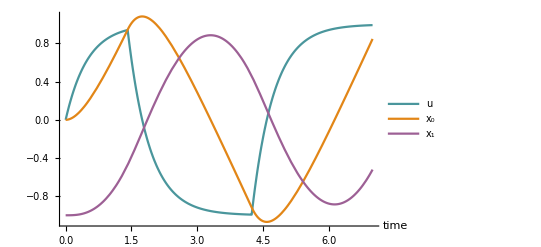

```mathematica
rank=3;
model={
(If[{0,1,0}.x[t]>1,-1,
If[{0,1,0}.x[t]<-1,1,
Clip[{0,-500,-1000}.x[t]]
]
]-{1,0,0}.x[t])2,
{1,0,0}.x[t],
{0,1,0}.x[t]};
te=7;
s=x[t]/.First[NDSolve[
{
x'[t]==model,
x[0]=={0,0,-1}
},x,{t,0,te}]];
name="PD delayed input";
p=Plot[{s[[1]],s[[2]],s[[3]]},{t,0,te},PlotRange->All,AxesLabel->{"time"},PlotLegends->legend,PlotStyle->colors]
savePdf[name, p];
```

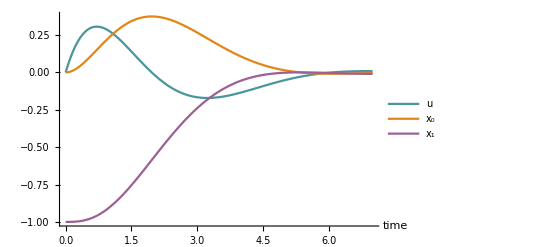

```mathematica
rank=3;
model={
(If[{0,1,0}.x[t]>1,-1,
If[{0,1,0}.x[t]<-1,1,
Clip[{0,-1.15,-0.5}.x[t]]
]
]-{1,0,0}.x[t])2,
{1,0,0}.x[t],
{0,1,0}.x[t]};
te=7;
s=x[t]/.First[NDSolve[
{
x'[t]==model,
x[0]=={0,0,-1}
},x,{t,0,te}]];
name="PD adjusted";
p=Plot[{s[[1]],s[[2]],s[[3]]},{t,0,te},PlotRange->All,AxesLabel->{"time"},PlotLegends->legend,PlotStyle->colors]
savePdf[name, p];
```

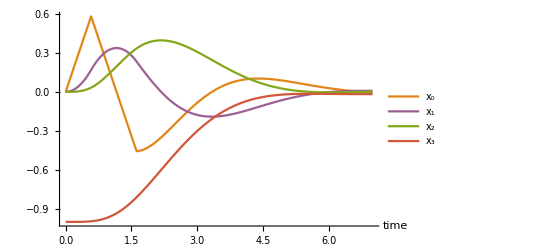

3.9

```mathematica
rank=4;
model={
If[{1,0,0,0}.x[t]>1,-1,If[{1,0,0,0}.x[t]<-1,1,Clip[1000({-0.5,-1,0,0}.x[t]+If[{0,0,1,0}.x[t]>1,-1,If[{0,0,1,0}.x[t]<-1,1,Clip[{0,0,-1.2,-0.5}.x[t]]]])]]],
{1,0,0,0}.x[t],
{0,1,0,0}.x[t],
{0,0,1,0}.x[t]
};
te=7;
x30=-1;
s=x[t]/.First[NDSolve[
{
x'[t]==model,
x[0]=={0,0,0,x30}
},x,{t,0,te}]];
name="PD cascade";
p=Plot[{s[[1]],s[[2]],s[[3]],s[[4]]},{t,0,te},PlotRange->All,AxesLabel->{"time"},PlotLegends->Drop[legend,1],PlotStyle->Drop[colors,1]]
savePdf[name,p];
For[tt=0,tt<te&&(s/.t->tt)[[4]]<x30/10,tt+=0.01,tt]
tt
```

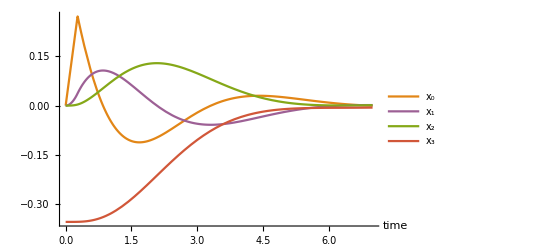

3.99

```mathematica
rank=4;
model={
If[{1,0,0,0}.x[t]>1,-1,If[{1,0,0,0}.x[t]<-1,1,Clip[1000({-0.5,-1,0,0}.x[t]+If[{0,0,1,0}.x[t]>1,-1,If[{0,0,1,0}.x[t]<-1,1,Clip[{0,0,-1.2,-0.5}.x[t]]]])]]],
{1,0,0,0}.x[t],
{0,1,0,0}.x[t],
{0,0,1,0}.x[t]
};
te=7;
x30=-0.35386002862997135;
s=x[t]/.First[NDSolve[
{
x'[t]==model,
x[0]=={0,0,0,x30}
},x,{t,0,te}]];
name="PD cascade small step";
p=Plot[{s[[1]],s[[2]],s[[3]],s[[4]]},{t,0,te},PlotRange->All,AxesLabel->{"time"},PlotLegends->Drop[legend,1],PlotStyle->Drop[colors,1]]
savePdf[name,p];
For[tt=0,tt<te&&(s/.t->tt)[[4]]<x30/10,tt+=0.01,tt]
tt
```

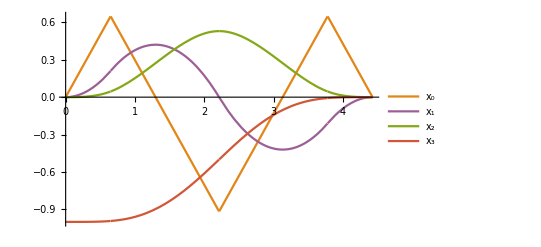

4.42671

```mathematica
t1= 1.54255;
u=Piecewise[{{1, t<1/t1}, {-1, t<2/t1+√2/t1}, {1, t<3/t1+2√2/t1}, {-1, True}}];
te=4/t1+2√2/t1;
x0=Integrate[u,t];
x1=Integrate[x0,t];
x2=Integrate[x1,t];
x3=Integrate[x2,t]-1;
x3/.t->te//N;
name="4th order reference";
p=Plot[{x0,x1,x2,x3},{t,0,te},PlotStyle->Drop[colors,1],PlotLegends->Drop[legend,1]]
savePdf[name,p];
te
```

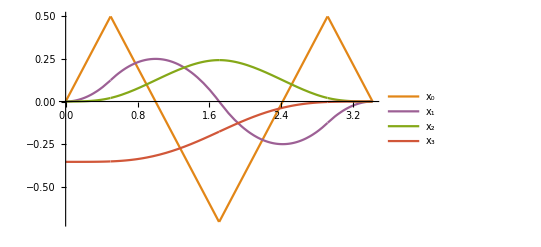

3.41421

2.43

```mathematica
t1= 2;
u=Piecewise[{{1, t<1/t1}, {-1, t<2/t1+√2/t1}, {1, t<3/t1+2√2/t1}, {-1, True}}];
te=4/t1+2√2/t1;
x0=Integrate[u,t];
x1=Integrate[x0,t];
x2=Integrate[x1,t];
x3=Integrate[x2,t]-0.35386002862997135;
x3/.t->te;
name="4th order reference small step";
p=Plot[{x0,x1,x2,x3},{t,0,te},PlotStyle->Drop[colors,1],PlotLegends->Drop[legend,1]]
savePdf[name,p];
te//N
For[tt=0,tt<te&&(x3/.t->tt)<-0.35386002862997135/10,tt+=0.01,tt]
tt
```

```mathematica
loadFile["O4c"];
For[i=1,i<Length[data[[2,5]]]&&data[[2,5,i,1,3]]<-0.35386002862997135/10,i+=1,i]
data[[2,5,i,1,1]]/10
```

2.60376

```mathematica
s=First[x/.DSolve[{x'[t]==ut-x[t],x[0]==0},x,t]];
First[ut/.Solve[s[2]==3/4]]//N
```

0.867388